```mathematica
time=Timing[
Size=100;
Tol=.01;
boundry=Table[Table[0,Size],Size];
values=boundry;
(*Set Boundaries*)
values[[All,1]]=100;boundry[[All,1]]=1;
values[[All,Size]]=100;boundry[[All,Size]]=1;
values[[1,All]]=0;boundry[[1,All]]=1;
values[[Size,All]]=0;boundry[[Size,All]]=1;
Change=100;

passes=0;
While[Change>Tol,
Change=0;
For[j=1,j≤Size,j++,
For[k=1,k≤Size,k++,
If[boundry[[j,k]]==0,
Avg=0;
by=0;
If[j>1,Avg+=values[[j-1,k]];by++];
If[j<Size,Avg+=values[[j+1,k]];by++];
If[k>1,Avg+=values[[j,k-1]];by++];
If[k<Size,Avg+=values[[j,k+1]];by++];
newChange=Abs[values[[j,k]]-Avg/by]//N;
If[Change<newChange,Change=newChange];
values[[j,k]]=Avg/by;]
]
]
passes++;
]

];
passes
time[[1]]*1000
Data=values//Flatten;
toPlot=Table[Table[0,3],Size*Size];
For[k=1,k<=Size*Size,k++,
	toPlot[[k,1]]=Floor[(k-1)/Size];
	toPlot[[k,2]]=Mod[k+Size-1,Size];
	toPlot[[k,3]]=Data[[k]];
]
toPlot//TableForm;
ListPlot3D[toPlot,PlotRange->All]
```

2085

2.15961×10^6

-Graphics3D-

```mathematica
"
```

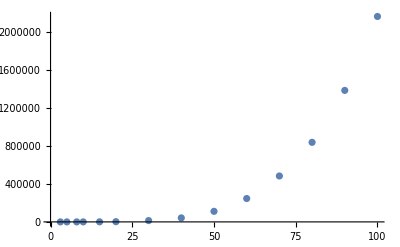

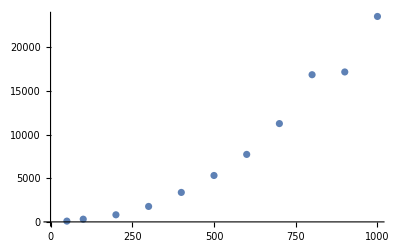

-Graphics-

```mathematica
size={3,5,8,10,15,20,30,40,50,60,70,80,90,100};
time={0,15.625,46.875,125,687.5,2265.63,13765.6,42078.1,111094,245750,482828,836359,1382280,2159610};
data={size,time}//Transpose;
ListPlot[data]
size={50,100,200,300,400,500,600,700,800,900,1000};
time={91,312,814,1772,3378,5320,7735,11268,16869,17185,23546};
data={size,time}//Transpose;
ListPlot[data]
```